# Symbolic Regression of Pendulum Data

## Introduction

## Lagrangians

### Euler Lagrange Equations

### Converting Expression from Cloure.

## Single Pendulum

### Theoretical Lagrangian

Theoretical single pendulum Lagrangian is of the form:

(L=1/2 mr^2(dθ/dt))^2-mgr(1-cosθ)

```mathematica
mass=1
length=1
gravity=1

simplepenlag[theta_,thetaprime_]:=(1/2*mass*length^2*thetaprime^2)-mass*gravity*length*(1-Cos[theta])
```

1

1

1

```mathematica
singpendata = Import["/Users/joelrussell/Documents/Imperial/Year_4/Masters_Project/Code/joel_flow/flow/data/mma_pendulum_large.csv"]

theta={#⟦1⟧&/@singpendata} 
thetaprime={#⟦2⟧&/@singpendata}
```

(2.98451 | -2.71051×10^-20
2.98137 | -0.0629866
2.97183 | -0.128468
2.95551 | -0.199029
2.93177 | -0.277437
2.89966 | -0.366729
2.85794 | -0.470298
2.805 | -0.591967
2.73881 | -0.736024
2.65689 | -0.907191
2.5563 | -1.11046
2.43357 | -1.35068
2.2848 | -1.63175
2.1058 | -1.95519
1.89244 | -2.31786
1.64127 | -2.70891
1.35043 | -3.10648
1.0209 | -3.47596
0.657662 | -3.77265
0.270325 | -3.95107
-0.127523 | -3.97952
-0.520366 | -3.85261
-0.893621 | -3.59364
-1.2361 | -3.2449
-1.54117 | -2.85281
-1.80653 | -2.45624
-2.03316 | -2.08159
-2.22407 | -1.74334
-2.38323 | -1.447
-2.51486 | -1.19244
-2.623 | -0.976402
-2.71127 | -0.79426
-2.78282 | -0.641007
-2.84028 | -0.511797
-2.88583 | -0.402177
-2.92123 | -0.308157
-2.94786 | -0.226199
-2.96677 | -0.153144
-2.97869 | -0.0861391
-2.98411 | -0.0225447
-2.98323 | 0.0401564
-2.97602 | 0.104449
-2.9622 | 0.172874
-2.94122 | 0.248123
-2.91225 | 0.333126
-2.87416 | 0.431139
-2.82547 | 0.545823
-2.76431 | 0.681297
-2.68837 | 0.842138
-2.59487 | 1.03327
-2.48054 | 1.25967
-2.34161 | 1.52569
-2.17399 | 1.83394
-1.97345 | 2.18326
-1.73621 | 2.56598
-1.45971 | 2.96452
-1.14376 | 3.34886
-0.791798 | 3.67723
-0.41175 | 3.90293
-0.0159409 | 3.98754
0.380495 | 3.91527
0.762308 | 3.69966
1.11687 | 3.37779
1.43588 | 2.99626
1.71557 | 2.59757
1.95587 | 2.21279
2.15922 | 1.86041
2.32932 | 1.54877
2.47039 | 1.27943
2.58654 | 1.05001
2.68158 | 0.856239
2.75881 | 0.69316
2.82107 | 0.555832
2.87068 | 0.439643
2.90956 | 0.340438
2.93921 | 0.254519
2.9608 | 0.178602
2.97517 | 0.109733
2.98289 | 0.045205
2.98427 | -0.0175317
2.97936 | -0.0809632
2.96797 | -0.1476
2.94964 | -0.22007
2.92367 | -0.301205
2.88901 | -0.394136
2.84433 | -0.502369
2.7879 | -0.629855
2.71757 | -0.781011
2.63074 | -0.960659
2.52432 | -1.17381
2.39471 | -1.42514
2.2379 | -1.71808
2.04969 | -2.05309
1.82604 | -2.42522
1.56385 | -2.82084
1.26192 | -3.21456
0.922251 | -3.56843
0.551103 | -3.83629
0.159321 | -3.97494
-0.238704 | -3.95912
-0.627423 | -3.79181)

(2.98451 | 2.98137 | 2.97183 | 2.95551 | 2.93177 | 2.89966 | 2.85794 | 2.805 | 2.73881 | 2.65689 | 2.5563 | 2.43357 | 2.2848 | 2.1058 | 1.89244 | 1.64127 | 1.35043 | 1.0209 | 0.657662 | 0.270325 | -0.127523 | -0.520366 | -0.893621 | -1.2361 | -1.54117 | -1.80653 | -2.03316 | -2.22407 | -2.38323 | -2.51486 | -2.623 | -2.71127 | -2.78282 | -2.84028 | -2.88583 | -2.92123 | -2.94786 | -2.96677 | -2.97869 | -2.98411 | -2.98323 | -2.97602 | -2.9622 | -2.94122 | -2.91225 | -2.87416 | -2.82547 | -2.76431 | -2.68837 | -2.59487 | -2.48054 | -2.34161 | -2.17399 | -1.97345 | -1.73621 | -1.45971 | -1.14376 | -0.791798 | -0.41175 | -0.0159409 | 0.380495 | 0.762308 | 1.11687 | 1.43588 | 1.71557 | 1.95587 | 2.15922 | 2.32932 | 2.47039 | 2.58654 | 2.68158 | 2.75881 | 2.82107 | 2.87068 | 2.90956 | 2.93921 | 2.9608 | 2.97517 | 2.98289 | 2.98427 | 2.97936 | 2.96797 | 2.94964 | 2.92367 | 2.88901 | 2.84433 | 2.7879 | 2.71757 | 2.63074 | 2.52432 | 2.39471 | 2.2379 | 2.04969 | 1.82604 | 1.56385 | 1.26192 | 0.922251 | 0.551103 | 0.159321 | -0.238704 | -0.627423)

(-2.71051×10^-20 | -0.0629866 | -0.128468 | -0.199029 | -0.277437 | -0.366729 | -0.470298 | -0.591967 | -0.736024 | -0.907191 | -1.11046 | -1.35068 | -1.63175 | -1.95519 | -2.31786 | -2.70891 | -3.10648 | -3.47596 | -3.77265 | -3.95107 | -3.97952 | -3.85261 | -3.59364 | -3.2449 | -2.85281 | -2.45624 | -2.08159 | -1.74334 | -1.447 | -1.19244 | -0.976402 | -0.79426 | -0.641007 | -0.511797 | -0.402177 | -0.308157 | -0.226199 | -0.153144 | -0.0861391 | -0.0225447 | 0.0401564 | 0.104449 | 0.172874 | 0.248123 | 0.333126 | 0.431139 | 0.545823 | 0.681297 | 0.842138 | 1.03327 | 1.25967 | 1.52569 | 1.83394 | 2.18326 | 2.56598 | 2.96452 | 3.34886 | 3.67723 | 3.90293 | 3.98754 | 3.91527 | 3.69966 | 3.37779 | 2.99626 | 2.59757 | 2.21279 | 1.86041 | 1.54877 | 1.27943 | 1.05001 | 0.856239 | 0.69316 | 0.555832 | 0.439643 | 0.340438 | 0.254519 | 0.178602 | 0.109733 | 0.045205 | -0.0175317 | -0.0809632 | -0.1476 | -0.22007 | -0.301205 | -0.394136 | -0.502369 | -0.629855 | -0.781011 | -0.960659 | -1.17381 | -1.42514 | -1.71808 | -2.05309 | -2.42522 | -2.82084 | -3.21456 | -3.56843 | -3.83629 | -3.97494 | -3.95912 | -3.79181)

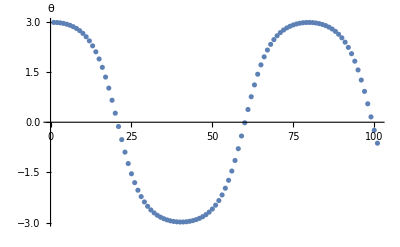

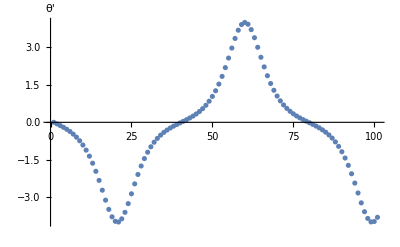

```mathematica
ListPlot[theta,AxesLabel->θ]
ListPlot[thetaprime,AxesLabel->θ']
```

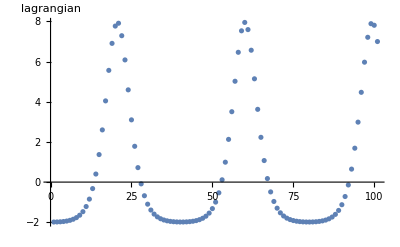

```mathematica
ListPlot[simplepenlag[theta,thetaprime],AxesLabel->lagrangian]
```

### Numerical Lagrangian Expressions

```mathematica
triallag1[theta_,omega_]:=Times[Times[0.022210588271571317, Plus[Plus[Plus[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Times[Cos[theta], 0.6247552574671112]], Cos[theta]], Times[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]]], omega], omega], Cos[theta]]], Sin[theta]]
```

SetDelayed::write: Tag List in («1»)(theta_,omega_) is Protected.

$Failed

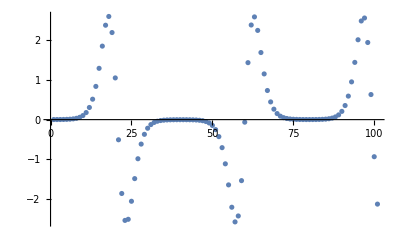

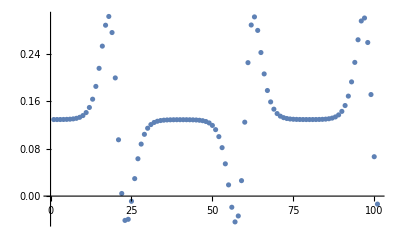

```mathematica
run1[theta_,omega_]:=Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12642579887098596], Times[omega, omega]]]]
run2[theta_,omega_]:=Times[Plus[Plus[Sin[theta], Subtract[Plus[Sin[theta], 1.9273329585287498], Sin[theta]]], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12641372676463694], Times[omega, omega]]]], 0.06703977631709543]

ListPlot[run1[theta,thetaprime]]
ListPlot[run2[theta,thetaprime]]
```

### Euler Lagrange Equations

```mathematica
Needs["VariationalMethods`"]
```

#### THEORETICAL

```mathematica
Clear[m,l,g]

m = 1
l = 1
g = 9.81

"Theoretical Values with Algebraic Representations of m g and l"

theorylag = 1/2 mr^2 θ'[t]^2+mgr(1-Cos[θ[t]])
theoryEL = EulerEquations[theorylag,θ[t],t]
theorysol = Solve[theoryEL,θ''[t]]


theorylagn = 1/2 m*r^2*θ'[t]^2+m*g*r*(1-Cos[θ[t]])
EulerEquations[theorylagn,θ[t],t]

theorysoln = DSolve[%,θ[t],t]

θ[t]/.theorysoln/.{C[1]->1,C[2]->1}

Plot[Evaluate[θ[t]/.theorysoln/.{C[1]->1,C[2]->1},{t,-10,10},PlotRange->All]]
```

1

1

9.81

Theoretical Values with Algebraic Representations of m g and l

mgr (1-cos(θ(t)))+1/2 mr^2 (θ'(t))^2

mgr sin(θ(t))-mr^2 θ''(t)==0

{{θ''(t)→(mgr sin(θ(t)))/mr^2}}

1/2 (θ'(t))^2+9.81 (1-cos(θ(t)))

9.81 sin(θ(t))-θ''(t)==0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t] -> -2. JacobiAmplitude[0.5 
 
                  2          2
       Sqrt[C[1] t  - 19.62 t  + 2. C[1] C[2] t - 39.24 C[2] t + 
 
                  2             2        39.24
         C[1] C[2]  - 19.62 C[2] ], -(------------)]}, 
                                      C[1] - 19.62
 
  {θ[t] -> 2. JacobiAmplitude[0.5 
 
                  2          2
       Sqrt[C[1] t  - 19.62 t  + 2. C[1] C[2] t - 39.24 C[2] t + 
 
                  2             2        39.24
         C[1] C[2]  - 19.62 C[2] ], -(------------)]}}
                                      C[1] - 19.62

{-2. 0.5 √(-18.62 t^2-37.24 t-18.62)2.10741,2. 0.5 √(-18.62 t^2-37.24 t-18.62)2.10741}

-Graphics-

```mathematica
"theorylag[mass_,length_,gravity_] := 1/2mass*length^2*"
```

theorylag[mass_,length_,gravity_] := 1/2mass*length^2*

#### EXPERIMENTAL

```mathematica
Clear[theta]

L= Times[Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.1264012221818857], Times[omega, omega]]]], 0.06703977631709543]

L = L/.omega->θ'[t]
L = L/.theta->θ[t]

ExpEL = EulerEquations[L,θ[t],t]

NDSolve[ExpEL,θ''[t]]

eom = θ''[t]/.%
```

0.0670398 (0.126401 omega^2 sin(theta)+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 sin(theta) (θ'(t))^2+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 (θ'(t))^2 sin(θ(t))+sin(θ(t))+sin(θ(t)) cos(θ(t)))

-0.0169478 θ''(t) sin(θ(t))-0.00847391 (θ'(t))^2 cos(θ(t))-0.0670398 sin^2(θ(t))+0.0670398 cos^2(θ(t))+0.0670398 cos(θ(t))==0

NDSolve[ExpEL,θ''[t]]

eom = θ''[t]/.%

## Double Pendulum